1. | 7.887024367×10^-13
1.000001×10^6 | -1.151856388×10^-15
2.000001×10^6 | -3.712308239×10^-16
3.000001×10^6 | 7.21644966×10^-16
4.000001×10^6 | -3.441691376×10^-15
5.000001×10^6 | 5.551115123×10^-16
6.000001×10^6 | 8.881784197×10^-16
7.000001×10^6 | -1.33226763×10^-15
8.000001×10^6 | 6.661338148×10^-16
9.000001×10^6 | -2.664535259×10^-15

1. | 2484.744256
1.000001×10^6 | 2.434752626×10^6
2.000001×10^6 | 3.443259186×10^6
3.000001×10^6 | 4.21711386×10^6
4.000001×10^6 | 4.869503648×10^6
5.000001×10^6 | 5.444270641×10^6
6.000001×10^6 | 5.963899749×10^6
7.000001×10^6 | 6.441748045×10^6
8.000001×10^6 | 6.886518402×10^6
9.000001×10^6 | 7.304255859×10^6

1. | 4919.495547
1.000001×10^6 | 4.869505134×10^6
2.000001×10^6 | 6.886518344×10^6
3.000001×10^6 | 8.434227503×10^6
4.000001×10^6 | 9.739006839×10^6
5.000001×10^6 | 1.088854058×10^7
6.000001×10^6 | 1.192779856×10^7
7.000001×10^6 | 1.288349493×10^7
8.000001×10^6 | 1.377303543×10^7
9.000001×10^6 | 1.460851014×10^7

4.8695×10^6

4.8695027×10^6

-Graphics3D-

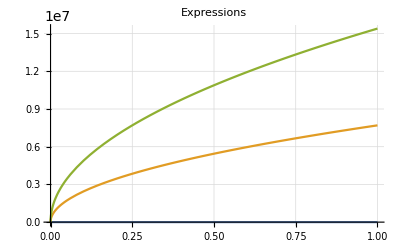

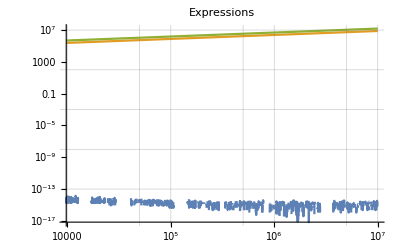

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Export::noopen: Cannot open ММиАвАП/d1.xls.

$Failed

ММиАвАП/d2.xls

ММиАвАП/d3.xls

ММиАвАП/d.png

ММиАвАП/d3D.png

```mathematica
σ = 1000000;
μr = 50;
μ0 = 1.256*10^-6;
y = 5 * 10^-3;
μ = μr*μ0;

d1 = 0;
d2 = 50;
d3 = 100;

δ[ω_] := Sqrt[2/(ω*μ*σ)];
zM[ω_] := Abs[Sqrt[ω*μ/σ]];
zg[ω_] := Abs[ω*μ0*y];

A[d_, ω_] := 8.69*d/δ[ω];
B[d_, ω_] := 20* Log10[1 - ((zg[ω] - zM[ω])/(zg[ω] + zM[ω]))^2*Exp[-2*d/δ[ω]]];
R[ω_] := 20* Log10[(zg[ω] + zM[ω])^2/(4 * zg[ω] * zM[ω])];
S[d_, ω_] := A[d, ω] + B[d, ω] + R[ω];

digits = 10;
Grid[Table[{SetPrecision[ω, digits], SetPrecision[S[d1, ω], 10]}, {ω, 1, 10000000, 1000000}]]
Grid[Table[{SetPrecision[ω, digits], SetPrecision[S[d2, ω], 10]}, {ω, 1, 10000000, 1000000}]]
Grid[Table[{SetPrecision[ω, digits], SetPrecision[S[d3, ω], 10]}, {ω, 1, 10000000, 1000000}]]

Block[{$MaxExtraPrecision=200},N[S[d3, 1000000],50]]
SetPrecision[S[d3, 1000000], 10]

Plot3D[S[d, ω], {ω, 0, 10000000}, {d, 0,100}, AxesLabel->Automatic]
Plot[{S[d1, ω], S[d2, ω], S[d3, ω]}, {ω, 0, 10000000},PlotLabel->"Expressions", GridLines -> Automatic]
LogLogPlot[{S[d1, ω], S[d2, ω], S[d3, ω]}, {ω, 0, 10000000},PlotLabel->"Expressions", GridLines -> Automatic]

Export["ММиАвАП/d1.xls",Table[{ω, S[d1, ω]}, {ω, 0, 10000000, 1000000}]]
Export["ММиАвАП/d2.xls",Table[{ω, S[d2, ω]}, {ω, 1, 10000000, 1000000}]]
Export["ММиАвАП/d3.xls",Table[{ω, S[d3, ω]}, {ω, 1, 10000000, 1000000}]]

Export["ММиАвАП/d.png",Plot[{S[d1, ω], S[d2, ω], S[d3, ω]}, {ω, 0, 10000000},PlotLabels->"Expressions"]]
Export["ММиАвАП/d3D.png",Plot3D[S[d, ω], {ω, 0, 10000000}, {d, 0,100}]]
```